```mathematica
(* https://www.expii.com/solve/62/4 *)
(* La La Land was nominated for 14 Oscars which tied the record for most Oscar nominations. Let p be a random number sampled uniformly from[0,1] and say that La La Land had a p chance of winning each of its Oscars. Out of the 14 Oscars, it won 6.
Now, in a parallel universe La La Land gets an additional surprise nomination for a 15th Oscar,two days after the ceremony. Given that it has already won 6 Oscars,what is the probability that it wins that Oscar? *)
```

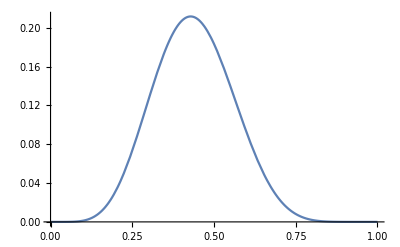

7/16

```mathematica
Clear[p];
n=14;
i=6;
(* The most probably p is 6/14 given past history... but it does not mean it is the true probability *)
Plot[Factorial[n]/(Factorial[n-i]*Factorial[i])*p^i*(1-p)^(n-i),{p,0,1}]
(* Since the probability distribution is binomial we need to calculate the weighted average of all the possible probabilites *)
Integrate[p*Factorial[n]/(Factorial[n-i]*Factorial[i])*p^i*(1-p)^(n-i),{p,0,1}]/Integrate[Factorial[n]/(Factorial[n-i]*Factorial[i])*p^i*(1-p)^(n-i),{p,0,1}]
```